```mathematica
func = InterpolatingPolynomial[{{0.41, 2.57418},{0.46, 2.32513}, {0.52,2.09336},{0.60,1.86203},{0.65,1.74926},{0.72,1.62098}}
,x]
```

1.62098+(-3.07484+(5.61099+(-12.2885+(18.8998-35.4119 (-0.65+x)) (-0.46+x)) (-0.6+x)) (-0.41+x)) (-0.72+x)

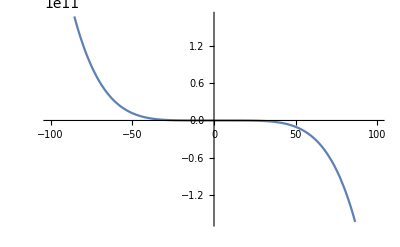

```mathematica
Plot[func, {x, -100, 100}]
```

```mathematica
Column[Table[N[func, 6], {x, 0.616, 0.616}]]
```

1.82369

```mathematica
Column[Table[N[func, 6], {x, 0.478,0.478}]]
```

2.24899

```mathematica
Column[Table[N[func, 6], {x, 0.665, 0.665}]]
```

1.71917